# Degree of Polarization

## Definitions

```mathematica
P [Ioff_,Iab_,Ia_,Ib_]:= Sqrt[(Ioff-Ia)*(Ioff-Ib)/(Ioff*Iab-Ib*Ia)]
ΔP [Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_]:=Sqrt[(((Ib (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2-(-Ib+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2ΔIa^2+(((Ia (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2-(-Ia+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2ΔIb^2+((-(Iab (-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)^2+(-Ia+Ioff)/(-Ia Ib+Iab Ioff)+(-Ib+Ioff)/(-Ia Ib+Iab Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff))))^2 ΔIoff^2+(-(Ioff (-Ia+Ioff) (-Ib+Ioff))/(2 √(((-Ia+Ioff) (-Ib+Ioff))/(-Ia Ib+Iab Ioff)) (-Ia Ib+Iab Ioff)^2))^2ΔIab^2]
e1 [Ioff_,Iab_,Ia_,Ib_] :=(Iab-Ib)/(Ioff-Ia)
Δe1[Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_] := Sqrt[(((Iab-Ib)/(-Ia+Ioff)^2)*ΔIa)^2 +((-1/(-Ia+Ioff))*ΔIb)^2 +((-(Iab-Ib)/(-Ia+Ioff)^2)*ΔIoff)^2 +((1/(-Ia+Ioff))*ΔIab)^2 ]
e2 [Ioff_,Iab_,Ia_,Ib_] :=(Iab-Ia)/(Ioff-Ib)
Δe2 [Ioff_,Iab_,Ia_,Ib_,ΔIoff_,ΔIab_,ΔIa_,ΔIb_]:= Sqrt[((-1/(-Ib+Ioff))*ΔIa)^2 +(((-Ia+Iab)/(-Ib+Ioff)^2)*ΔIb)^2 +((-(-Ia+Iab)/(-Ib+Ioff)^2)*ΔIoff)^2 +((1/(-Ib+Ioff))*ΔIab)^2 ]
Flipp[CountsOff_,CountsOn_]:=CountsOff/CountsOn
ErrFlipp[CountsOff_,CountsOn_,ΔCountsOff_,ΔCountsOn_]:= Sqrt[((-CountsOff/CountsOn^2)*ΔCountsOn)^2 + ((1/CountsOn)*ΔCountsOff)^2 ]
Contrast[Imax_,Imin_]:=(Imax-Imin)/(Imax+Imin)
ErrContrast[Imax_,Imin_,ΔImax_,ΔImin_]:=Sqrt[(((2*Imin)/(Imax+Imin)^2)*ΔImax)^2+(((-2*Imax)/(Imax+Imin)^2)*ΔImin)^2]
k1[e_]:=1/2(e+1)
k2[e_]:=1/2(e+1)
Δk1[Δe_]:=1/2Δe
Δk2[Δe_]:=1/2Δe
```

## File input

Intro

```mathematica
Needs["ErrorBarPlots`"]
```

The following code will calculate all degrees of polarisation of all files in the folder matching the criteria below. All the files should have been created with the Polarimeter VI containing multiple degrees of polarisation measurements for different positions in one file.

File Import

Importing all files that match a certain string.

```mathematica
(* get all files that matter in directory and import them all *)
files=FileNames["*-degree-of-polarisation*.dat",NotebookDirectory[]]
positions=Import[NotebookDirectory[]<>"2018-11-23-0900-degree-of-polarisation.pos","Table"][[1]][[;;;;4]];
data=Import[#]&/@files;
```

{C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 23.11.2018\2018-11-23-1325-degree-of-polarisation.dat}

Calculations & Rearrangements

Degree of Polarization

```mathematica
(* get the interesting intensities *)
intensities=Transpose[#[[5;;-1]]][[2]]&/@data;
intensities=Partition[#,4]&/@intensities;

(* rearrange the items to match with the required form of P [Ioff_,Iab_,Ia_,Ib_]
if measurement is sorted differently *)
Rearrange1[item_]:=item[[{1,4,2,3}]]
intensities=Map[Rearrange1,#]&/@intensities;
```

```mathematica
(* calculating the degree of polarisation for all entries *)
pol = P@@@#&/@intensities //N //Re;
(* calculate sqrt for deltas and joining the lists, then calculating deviations *)
pDelta=ΔP @@@#&/@Join[intensities,Sqrt[intensities],3] //N;
pDelta=Re[pDelta];
(* writing the degree of polarisation and its deviation into array 
with touples of (pol, dev) *)
p=Riffle@@@Transpose[{Re[pol],Map[ErrorBar,Re[#]]&/@pDelta}];
(* p=Riffle@@@Transpose[{Re[pol],Re[#]&/@pDelta}]; *)
p=Partition[#,2]&/@p;

(* add the positions to the data *)
buff1=Partition[#,2]&/@(Riffle[positions,#]&/@pol);
buff2=Map[ErrorBar,#]&/@pDelta;
p=Riffle@@@Transpose[{buff1,buff2}];
p=Partition[#,2]&/@p;

(* transmissions *)
transmission=(Flatten[#][[;;;;4]]&/@intensities);

(* transmission deviations not normalized *)
(* transmissionD=Sqrt[#]&/@transmission; *)
(* normalized transmission deviations *)
transmissionD=Sqrt[#]/Max[#]&/@transmission;

(* normalization *)
transmission=#/Max[#]&/@transmission;

(* add the positions to the transmission *)
buff1=Partition[#,2]&/@(Riffle[positions,#]&/@transmission);
buff2=Map[ErrorBar,#]&/@transmissionD;
t=Riffle@@@Transpose[{buff1,buff2}];
t=Partition[#,2]&/@t;
```

Efficiencies

```mathematica
efficency1=e1@@@#&/@intensities//N;
efficency2=e2@@@#&/@intensities//N;
efficency1Delta=Δe1 @@@#&/@Join[intensities,Sqrt[intensities],3] //N;
efficency1Delta=Re[efficency1Delta];
efficency2Delta=Δe2 @@@#&/@Join[intensities,Sqrt[intensities],3] //N;
efficency2Delta=Re[efficency2Delta];

(*eff1=Riffle@@@Transpose[{Re[efficency1],Map[ErrorBar,Re[#]]&/@efficency1Delta}];
eff1=Partition[#,2]&/@eff1;
eff2=Riffle@@@Transpose[{Re[efficency2],Map[ErrorBar,Re[#]]&/@efficency2Delta}];
eff2=Partition[#,2]&/@eff2;*)

effbuff1=Partition[#,2]&/@(Riffle[positions,#]&/@efficency1);
effbuff2=Map[ErrorBar,#]&/@efficency1Delta;
efficency1=Riffle@@@Transpose[{effbuff1,effbuff2}];
efficency1=Partition[#,2]&/@efficency1;

effbuff1=Partition[#,2]&/@(Riffle[positions,#]&/@efficency2);
effbuff2=Map[ErrorBar,#]&/@efficency2Delta;
efficency2=Riffle@@@Transpose[{effbuff1,effbuff2}];
efficency2=Partition[#,2]&/@efficency2;
```

Plots

List of plots of different measurements:

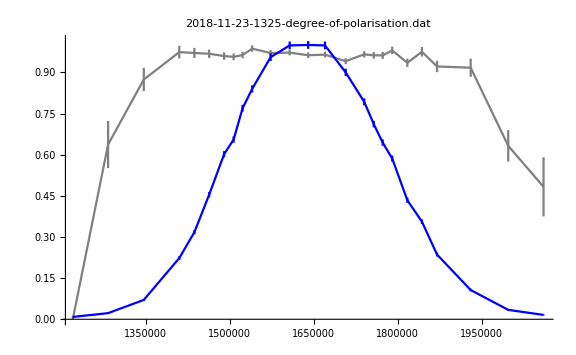

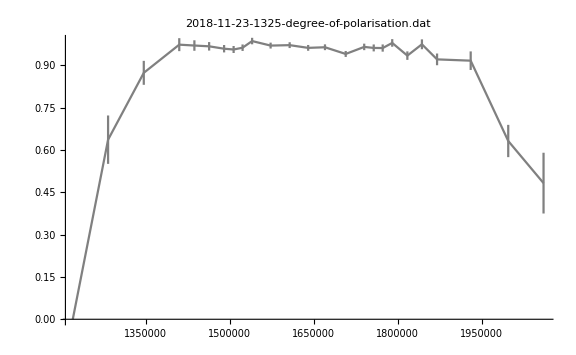
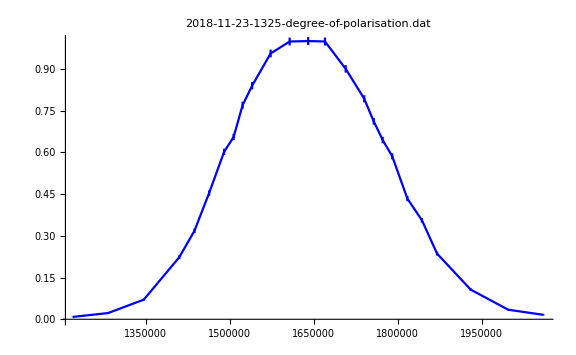
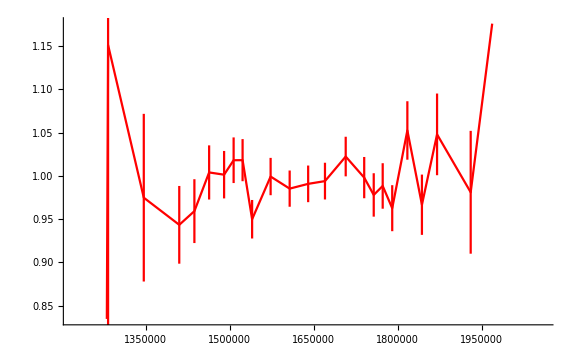
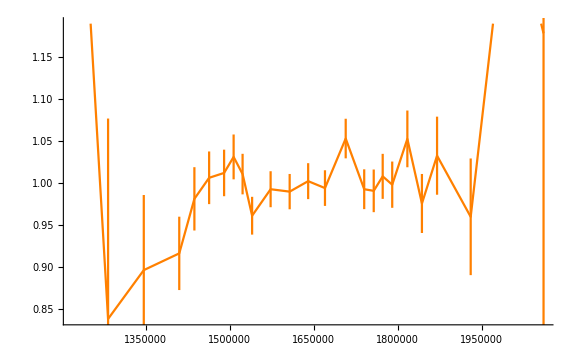

```mathematica
(* plotting specified files without correct x-axis values *)
listOfPlots={1};
pPlots=ErrorListPlot[p[[#]],PlotStyle->Gray,Joined->True,PlotLabel->FileNameTake[files[[#]]],ImageSize->Large]&/@listOfPlots;
tPlots=ErrorListPlot[t[[#]],PlotStyle->Blue,Joined->True,PlotLabel->FileNameTake[files[[#]]],ImageSize->Large]&/@listOfPlots;
e1Plots=ErrorListPlot[efficency1[[#]],PlotStyle->Red,Joined->True,ImageSize->Large]&/@listOfPlots;
e2Plots=ErrorListPlot[efficency2[[#]],PlotStyle->Orange,Joined->True,ImageSize->Large]&/@listOfPlots;

Show[pPlots[[#]],tPlots[[#]],PlotRange->All]&/@listOfPlots
{pPlots[[1]],tPlots[[1]],e1Plots[[1]],e2Plots[[1]]}
```

Closer Examination of DC1 & DC2 (moved to a separate notebook)

Here we’ll take a closer look at the two DC coils.

```mathematica
measurementNumber=1;
dataDC1=Transpose[intensities[[measurementNumber]]][[3]];
dataDC2=Transpose[intensities[[measurementNumber]]][[4]];
```

```mathematica
Contrast[Max[dataDC1],Min[dataDC1]]
Contrast[Max[dataDC2],Min[dataDC2]]
ErrContrast[Max[dataDC1],Min[dataDC1],Sqrt[Max[dataDC1]],Sqrt[Min[dataDC1]]]
ErrContrast[Max[dataDC2],Min[dataDC2],Sqrt[Max[dataDC2]],Sqrt[Min[dataDC2]]]
```

0.627244

0.728277

0.0506167

0.0424689

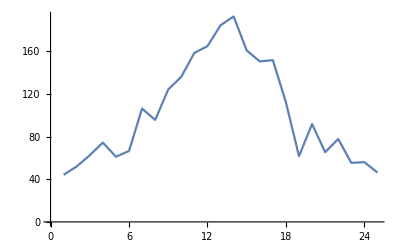

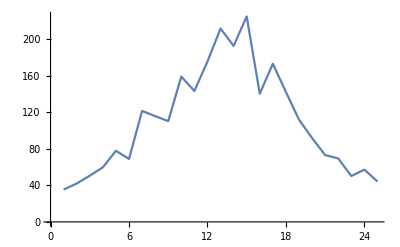

```mathematica
ListLinePlot[dataDC1]
ListLinePlot[dataDC2]
```